```mathematica
Clear[coord, metric,inversemetric, affine,r,θ,ϕ,t] (* clear vals from kernel *)
```

```mathematica
n=4
```

4

```mathematica
coord = {r,θ,ϕ,t} (* define coords.... yes t = x^4, fight me *)
```

{r,θ,ϕ,t}

```mathematica
f:= 1-(2*M)/r (* metric functions *)
h:= 1+(26*M)/r+(66*M^2)/(5*r^2)+(96*M^3)/(5*r^3)-(80*M^4)/r^4
k:= 1 + M/r+(52*M^2)/(3*r^2)+(2*M^3)/r^3+(16*M^4)/(5*r^4)-(368*M^5)/(3*r^5)
Subscript[g, tt] = -f * (1+H)
Subscript[g, rr] = 1/f*(1 + K)
H:= x/(3*f)*(M/r)^3*h (* actual metric functions, taken from Yunes & Stein 2011. x = ζ *)
K:=-(x/f)*(M/r)^2*k
rH=2M-49/40*M*x;
fR := 1 - rH/r
Subscript[gR, tt]= -fR * (1+H+HR);
Subscript[gR, rr]=1/fR*(1 + K+KR);
HRsub=HR->Series[HR/.Solve[(Series[Subscript[g, tt]-Subscript[gR, tt],{x,0,1}]//Normal)==0,HR][[1]],{x,0,1}]//Normal//Simplify
KRsub=KR->Series[KR/.Solve[(Series[Subscript[g, rr]-Subscript[gR, rr],{x,0,1}]//Normal)==0,KR][[1]],{x,0,1}]//Normal//Simplify
```

(1+H) (-1+(2 M)/r)

(1+K)/(1-(2 M)/r)

HR→(49 M x)/(80 M-40 r)

KR→-(49 M x)/(80 M-40 r)

```mathematica
metric=Simplify[{{Subscript[gR, rr],0,0,0}, {0, r^2 , 0, 0}, {0,0, r^2 Sin[θ]^2,0}, {0,0,0,Subscript[gR, tt]}}/.{HRsub,KRsub}, {r >0, M==1}] (* metric! *)
```

{{(120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x)/(3 r^5 (-80+40 r+49 x)),0,0,0},{0,r^2,0,0},{0,0,r^2 Sin[θ]^2,0},{0,0,0,-((-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x))/(4800 r^7)}}

```mathematica
metric//MatrixForm
```

((120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x)/(3 r^5 (-80+40 r+49 x)) | 0 | 0 | 0
0 | r^2 | 0 | 0
0 | 0 | r^2 Sin[θ]^2 | 0
0 | 0 | 0 | -((-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x))/(4800 r^7))

```mathematica
inversemetric=Simplify[Inverse[metric]] (* invert *)
```

{{(3 r^5 (-80+40 r+49 x))/(120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x),0,0,0},{0,1/r^2,0,0},{0,0,Csc[θ]^2/r^2,0},{0,0,0,-(4800 r^7)/((-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x))}}

```mathematica
inversemetric//MatrixForm
```

((3 r^5 (-80+40 r+49 x))/(120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x) | 0 | 0 | 0
0 | 1/r^2 | 0 | 0
0 | 0 | Csc[θ]^2/r^2 | 0
0 | 0 | 0 | -(4800 r^7)/((-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x)))

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coord[[k]] ]+
D[metric[[s,k]],coord[[j]] ]-D[metric[[j,k]],coord[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}],{r>0}](* calc christoffels *) /.θ-> Pi/2
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | (-4800 r^6-6960 r^5 x+18400 x (-80+49 x)-21 r^4 x (320+203 x)-4 r^3 x (-37040+2793 x)+64 r x (5080+5341 x)+4 r^2 x (38480+29841 x))/(r (-80+40 r+49 x) (120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x))
Γ[1, 2, 2] | -(3 r^6 (-80+40 r+49 x))/(120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x)
Γ[1, 3, 3] | -(3 r^6 (-80+40 r+49 x))/(120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x)
Γ[1, 4, 4] | ((-80+40 r+49 x) (4800 r^6+7203 r^5 x^2-5600 x (-80+49 x)+20 r^2 x (-2640+343 x)-96 r x (960+637 x)+8 r^3 x (-10400+6713 x)+3 r^4 x (-800+7203 x)))/(1600 r^3 (120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x))
Γ[2, 2, 1] | 1/r
Γ[3, 3, 1] | 1/r
Γ[4, 4, 1] | (4800 r^6+7203 r^5 x^2-5600 x (-80+49 x)+20 r^2 x (-2640+343 x)-96 r x (960+637 x)+8 r^3 x (-10400+6713 x)+3 r^4 x (-800+7203 x))/(r (-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x))

Using decimal powers here gets rid of square roots, which python cannot parse into mathematical functions.

```mathematica
Subscript[u, r]= Simplify[(-1(1 + inversemetric[[4,4]])/inversemetric[[1,1]])^(.5), r> rH] (* calc radial infall velocity of gas to O(x)*)
```

0.57735 (-1/(r^5 (-80+40 r+49 x))(120 r^6-7360 x-3488 r x-1624 r^2 x+228 r^3 x+174 r^4 x+147 r^5 x) (1-(4800 r^7)/((-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x))))^0.5

```mathematica
Subscript[(u^t), stat]=Simplify[(-1/metric[[4,4]])^(.5), r> rH] (* camera velocity, to O(x) *)
```

69.282 (r^7/((-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x)))^0.5

```mathematica
Subscript[u, t,stat]=Simplify[(-1/inversemetric[[4,4]])^(0.5), r> rH]
```

0.0144338 (((-80+40 r+49 x) (120 r^6+1600 x+416 r x-56 r^2 x-548 r^3 x-294 r^4 x-147 r^5 x))/r^7)^0.5

```mathematica
Collect[Normal[Series[(Subscript[u, t,stat])^2/r^4,{x,0,1}]]//Simplify,x]
```

(-2+r)/r^5+((-400+96 r+66 r^2+130 r^3+5 r^4) x)/(15 r^11)

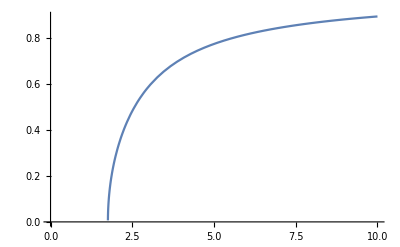

```mathematica
Plot[Simplify[Subscript[u, t,stat], x==0.2],{r,0.,10.}]
```

```mathematica
txtfile = OpenWrite["~/Research/Graduate/YunesGammie/BHShadow/Programs/RayTrace_Intensity/mathematica/SGBEquations.txt", FormatType->OutputForm] (* write everything to a text file *)
```

OutputStream[…]

```mathematica
WriteString[txtfile, ToString[metric[[4,4]]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""] (* silly way to insert a linebreak :) *)
WriteString[txtfile, ToString[metric[[1,1]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[metric[[2,2]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[metric[[3,3]]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[inversemetric[[4,4]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[inversemetric[[1,1]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[inversemetric[[2,2]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[inversemetric[[3,3]]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""]
```

```mathematica
WriteString[txtfile, ToString[affine[[4,4,1]]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[affine[[1,4,4]]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[affine[[1,1,1]]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[affine[[1,2,2]]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[affine[[1,3,3]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[affine[[2,2,1]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[affine[[3,3,1]] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[Subscript[u, r] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[Subscript[(u^t), stat] /.θ-> Pi/2// InputForm]]
Write[txtfile, ""]
WriteString[txtfile, ToString[Subscript[u, t,stat]/.θ-> Pi/2 // InputForm]]
Write[txtfile, ""]
```

```mathematica
Close[txtfile]
```

/Users/adam.bauer/Research/Graduate/YunesGammie/BHShadow/Programs/RayTrace_Intensity/mathematica/SGBEquations.txt